## Fig. S3B-D

Generate plots showing how eigenvalues scale with diffusion time tau_D. This example illustrates the emergence of the slow manifold with a relaxation time 1/tau_D.

```mathematica
Clear["Global`*"]; 
precision=60;
$MinPrecision=precision;
SetDirectory[NotebookDirectory[]];
```

### Statics, general p

```mathematica
getPositions[pop0_]:=
Block[{m0,list,extendedPop},
m0=Length[pop0];
extendedPop=Join[{0},pop0];
Table[{Total[extendedPop[[1;;i-1]]],Total[extendedPop[[1;;i]]]},{i,2,m0+1}]
];

getConcentration[n_,nutrient_]:=
Block[{i,m0,c,dc,m,cSys,cSysWrap,cSystem,dcSys,dcSysWrap,dcSystem,totalcSys,vars,aVars,bVars,z},
m0=Length[n];
aVars=ToExpression[Table["a"<>IntegerString[k],{k,m0}]];
bVars=ToExpression[Table["b"<>IntegerString[k],{k,m0}]];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
dc[a_,b_,α_,θ_]:=Sqrt[α/d]*(a*E^(Sqrt[α/d]*θ)-b*E^(-Sqrt[α/d]*θ));

(*  Create a system of eqs for c(θ) in each region *)
cSys=Table[c[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==c[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
cSysWrap=c[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==c[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
cSystem=Join[cSys,{cSysWrap}];

(*do the same thing for the derivatives of c(θ)*)
dcSys=Table[dc[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==dc[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
dcSysWrap=dc[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==dc[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
dcSystem=Join[dcSys,{dcSysWrap}];

totalcSys=Join[cSystem,dcSystem];
vars=Table[{aVars[[i]],bVars[[i]]},{i,m0}]//Flatten;
{z,m}=CoefficientArrays[totalcSys,vars];
LinearSolve[N[m,precision],N[-z,precision]]  
];
```

### Define some constants

```mathematica
supply=1;  (*total nutrient supply*)
δ=supply;
e=1;             (* total enzyme budget*)
baseSteps=1000000;
```

### Numeric parameters

```mathematica
SeedRandom[340]
s={1/2,1/2};
p=Length[s];
```

```mathematica
alphas={.45,.55,.6};
α=Table[{alphas[[i]],e-alphas[[i]]},{i,Length[alphas]}];
m=Length[α];
strat=Table[α[[i,1]],{i,m}];   (*maps strategies to continuum of nutrient 1, nutrient 2*)
sScaled=(e/Total[s])*s[[1]];
```

```mathematica
varList=Table["n"<>ToString[i]//ToExpression,{i,m}];
```

```mathematica
colors=Table[ColorData[97,i],{i,m}];
graphic=Table[{Graphics[{EdgeForm[{Black}],FaceForm[colors[[i]]],Disk[]}],.05},{i,m}];
```

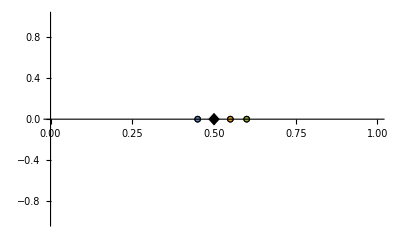

```mathematica
Show[ListPlot[Table[{{strat[[i]],0}},{i,m}],Axes->{True,False},AxesStyle->Thick,Ticks->{0,.2,.4,.6,.8,1},TicksStyle->Directive[Black, 12],PlotMarkers->graphic,PlotRange->{{0,1},Automatic}],Graphics[{EdgeForm[{White}],Polygon[{{.5-.02,0},{.5,.07},{.5+.02,0},{.5,-.07}}]}],Method->{"AxesInFront"->False}]
```

```mathematica
Export["figS3_strategies.svg",%];
```

### dynamics, general p

```mathematica
getGrowth[pop_,species_,c_]:=
Block[{growth,myN,myA,myB},
myN=pop[[species]];
myA=c[[species*2-1]];
myB=c[[species*2]];

growth=Table[α[[species,i]]*((s[[i]]*myN/α[[species,i]])+Sqrt[d/α[[species,i]]]*(myA[[i]]*(E^(myN*Sqrt[α[[species,i]]/d])-1)-myB[[i]]*(E^(-myN*Sqrt[α[[species,i]]/d])-1))),{i,p}]//Total
];
```

```mathematica
ndot[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0=n;
cCoeff=Transpose[Table[getConcentration[n0,v],{v,p}]];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0
];

ndotComponent[n_?(VectorQ[#, NumericQ]&),sigma_]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0=n;
cCoeff=Transpose[Table[getConcentration[n0,v],{v,p}]];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0;
dn[[sigma]]
];
```

```mathematica
nDotGeneralM[n0_,species_]:=
Block[{},
input=n0;
cCoeff=Transpose[Table[getConcentration[n0,v],{v,p}]];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
dn=growthTable-δ*n0;
dn[[species]]
]
```

```mathematica
partialDerivative[n_,σ_,ν_]:=
Block[{},
deriv=N[D[nDotGeneralM[{##},σ]&@@(#&/@varList),varList[[ν]]],precision];
rules=Table[varList[[i]]->n[[i]],{i,m}];
deriv/.rules
];
```

### find eigenvalues iteratively

```mathematica
randomInit[n_]:=RandomPoint[Simplex[l*IdentityMatrix[m]],n];
```

```mathematica
dSet={10^4,10^3,10^2,10^1,1};
lSet={1,1,1,1,1};
spaceSet=Table[{dSet[[i]],lSet[[i]]},{i,Length[dSet]}];
```

```mathematica
tauSquared=Table[e*lSet[[i]]^2/dSet[[i]],{i,Length[dSet]}];
```

```mathematica
tau=Sqrt[tauSquared];
```

```mathematica
numTrials=Length[spaceSet];
sols=ConstantArray[0,numTrials];
fixedPoints=ConstantArray[0,numTrials];
eigenSystems=ConstantArray[0,numTrials];
singularValues=ConstantArray[0,numTrials];
```

```mathematica
For[i=1,i≤numTrials,i++,
d=spaceSet[[i,1]];
l=spaceSet[[i,2]];
nInit=l*ConstantArray[1/m,m];
steps=d*baseSteps;
sol=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit},n,{t,0,steps}];
fixedPoints[[i]]=sol[sol["Domain"][[1,2]]];
sols[[i]]=sol;


jacobian[n_]:=Table[partialDerivative[n,i,j],{i,m},{j,m}];
eigenSystems[[i]]=Eigensystem[jacobian[fixedPoints[[i]]]];

singularValues[[i]]=SingularValueList[jacobian[fixedPoints[[i]]]];
];
```

### Plotting and analysis

```mathematica
scalePlots=ConstantArray[0,m];
logSpacePlots=ConstantArray[0,m];
```

```mathematica
For[i=1,i≤m,i++,

orderedPairs=Transpose[{tauSquared,Abs[Re[eigenSystems[[;;,1,i]]]]}];
scalePlots[[i]]=ListLogLogPlot[orderedPairs];

logFit=LinearModelFit[Log[orderedPairs],x,x];
params=logFit["BestFitParameters"];
logSpacePlots[[i]]=Show[LogLogPlot[E^(params[[1]])*x^(params[[2]]),{x,5*10^-5,1.2},PlotStyle->Directive[Dashed,Black],PlotLabel->"η = "<>ToString[Round[params[[2]],.1]]<>"0",LabelStyle->Directive[FontFamily["Helvetica"],12,Black],PlotRange->{Automatic,Automatic}],ListLogLogPlot[orderedPairs,PlotMarkers->{Automatic,12}],TicksStyle->Directive[Black, 12]]

]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

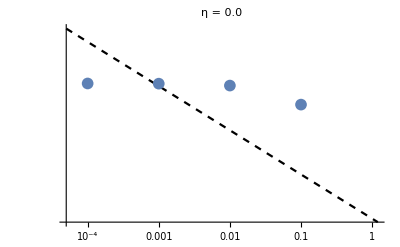
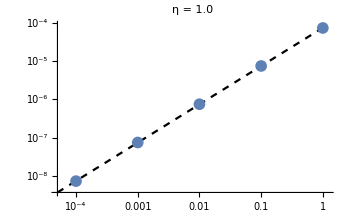
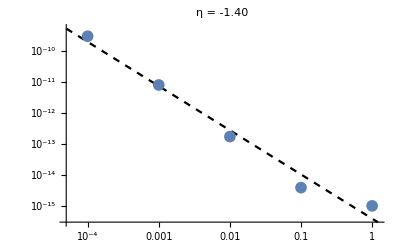

```mathematica
logSpacePlots
```

```mathematica
figNames={"B","C","D"};
```

```mathematica
For[i=1,i≤m,i++,
Export["figS3"<>figNames[[i]]<>"_eigenvalueScaling.svg",logSpacePlots[[i]]];]
```